```mathematica
Clear[glConstMinSquaredDistanceFromOrigin,glConstMinAngleBetweenLatticeVectors,glConstLocDefault,glConstDefaultMass,glConstKDefaults,glConstKMin,glConstKMax,glConstMMax,glConstWindowHalfWidth,glConstSpringColors,glConstPrimaryDisplaySize,glConstTextDisplayOffsetHack,glConstNeighboringCellIndexes,glConstDynPlotRange,glConstSpringColorsByN(*, glInitDone*)];

glConstMinSquaredDistanceFromOrigin = 0.1 ;
glConstMinAngleBetweenLatticeVectors=Pi/6;
glConstLocDefault={{0.1,1.3},{1.9,0.8}};
glConstDefaultMass=20;
glConstKDefaults={0.25,0.25,0.25,0.25,0.25};
glConstKMin=0.05;
glConstKMax=1;
glConstMMax=30;
glConstWindowHalfWidth=3;
glConstSpringColors=Darker@{Orange,Green,Purple,Cyan,Yellow};
glConstPrimaryDisplaySize={380,380};
glConstTextDisplayOffsetHack={0.25,0.25};
glConstNeighboringCellIndexes={{1,0},{0,1},{1,1},{1,-1}};
glConstDynPlotRange = {{-glConstWindowHalfWidth/2, glConstWindowHalfWidth}, {-glConstWindowHalfWidth/2, glConstWindowHalfWidth}} ;

(*
{{-1,0}->RGBColor[...],{0,-1}->RGBColor[...], ...}
*)
glConstSpringColorsByN = DeleteDuplicates@Flatten[Table[s Append[glConstNeighboringCellIndexes,{0,0}][[n]] -> glConstSpringColors[[n]], {s, -1, 1, 2}, {n, 5} ],1] ;

(*
Future possible maintainance TODOs:
{{implement a min separation for the equilibrium mass positions too (as done for the lattice vectors). 
Trickier, since that should be based on the separations in the origin cell, 
and not the obsolute separations of the locators.
Even if that is done, that doesn't mean that the scaling won't allow for overlap in the dynamic tab.}, {would be cool to make qLoc a pair of Locators that:
 trace out constrained positions along the 2 Pi scaled reciprocal lattice vectors.
(returning the distance from the origin of each of those locators)}, {a message box on user error:
- when an angle or distance from origin change has driven a reset of the lattice vectors.
- when too many of the locators have been deleted and a forced reset to the defaults occurs.}, {some of the ::usage = "" strings are now out of date}, {usage strings could probably now be un- commented-out.  
Will that re-introduce the problems on submission that were seen when the usage strings were in the Initiialzation block?}, {Can the frequency qPlaneLoc LocatorPane look more like Slider2D in the dynamics tab for consistency?}, {Am using a calculated value for the max freq for the freq plot intersection plane. 
Hardcoded this to magic # that's out of the graphic (23), but that could be wrong for some params}, {Scaling of the masses ended up different for the dynPlot vs. parameters tab. 
Hacked the dynPlot scaling for now, to be a bit closer.}}
*)

ClearAll[checkAgainstRange] ;
(*checkAgainstRange::usage = "This is to deal with InputForm Manipulators, that allow non-numeric values to be passed, or values that exceed the range specified in the Manipulator." ;*)
checkAgainstRange[v_,default_,lowerLimit_, upperLimit_] := 
Module[{result},
result = If [ NumberQ[v],v, default] ;

result = If [ result <= upperLimit, result,default ] ;
result = If [ result >= lowerLimit, result,default ] ;

result
] ;

ClearAll[springPoints] ;
(* Based on my ListLinePlot answer posted in: http://mathematica.stackexchange.com/a/37228/10 *)
(*
springPoints::usage = "springPoints[ {point1, point2}, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{{1,2},{3,5}}], AspectRatio→Automatic, PlotStyle -> Darker[ Purple ] ]" ;*)

springPoints[ a12_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{a1, a2, n1, springDiff, nd, r, r1 },
{a1, a2} = a12 ;
n1 = Norm[a1] ;
springDiff = a2 - a1 ;
nd = Norm[springDiff] ;
r = RotationMatrix[ArcTan @@  springDiff ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
] ;

ClearAll[indexLabel] ;
(*
indexLabel::usage = "k_i(or other character) in italic. indexLabel['k', 1]" ;
*)
indexLabel = Subscript[Style[#1,Italic], #2] & ;

ClearAll[kLable] ;
(*
kLable::usage = "k_i(or other character) in italic and colored by spring index. kLable[k]" ;
*)
kLable = Style[ indexLabel["k", #], FontColor->glConstSpringColors[[#]] ] & ;

ClearAll[ massColors ] ;
massColors := ( Darker[{ Blue, Green, Purple, Red, Orange }][[Mod[#, 5] + 1] ] & );

ClearAll[ massLabel ] ;
massLabel := Style[indexLabel["m", #], massColors[#]] & ;

ClearAll[calcLineTable];
calcLineTable[ n_List, b_List, i_List ] :=Module[{first, second},
{first, second} = i ;
Table[
Line[
{-n[[first]]b[[first]] + j b[[second]],n[[first]]b[[first]] + j b[[second]]} 
] 
, {j, -n[[second]], n[[second]]}
]
] ;

ClearAll[calcReciprocalBasis];
(*
calcReciprocalBasis::usage = "Return a reciprocal frame basis for a set of vectors.  This doesn't include the 2 π scaling that is common in solid state physics.  Example, displaying the desired Kronicker delta behaviour:

b = {{2,1},{-1/4, 2}} ;
g = calcReciprocalBasis[ b ] ;

{g[[1]].loc[[1]],
g[[1]].loc[[2]],
g[[2]].loc[[1]],
g[[2]].loc[[2]]}
" ;
*)
calcReciprocalBasis[loc_List] := Inverse[ Transpose[ loc ] ] ;

ClearAll[pointsTable];
pointsTable[ mPosFirstCell_List, latticeBasis_List, numberLatticeLinesToDisplay_List ] := Table[ 
mPosFirstCell + {i,j}. latticeBasis
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] ;

ClearAll[nMassesFromLocArray];
nMassesFromLocArray[uLoc_] := ((Dimensions[uLoc] // First) -2) ;

ClearAll[adjustedmoSel];
adjustedmoSel[rNumM_,mOrigInd_,m1Ind_]:=If[rNumM>2,
If[ mOrigInd==m1Ind,
First[DeleteCases[Range[rNumM],m1Ind]],
mOrigInd 
],
First@Delete[Range[2],m1Ind]
];

ClearAll[constructKArrayElements];
constructKArrayElements[ i_Integer, j_Integer  ] := Module[{a},
a = Flatten[Table[{i, j, s glConstNeighboringCellIndexes[[n]]} -> glConstKDefaults[[n]], {s, -1, 1, 2}, {n, 4} ], 1] ;

If [ i < j, Append[a,{i,j,{0,0}} -> glConstKDefaults[[5]]], a ] 
] ;

ClearAll[constructKArray];
constructKArray[ r_Integer ] := Flatten[Table[constructKArrayElements[i,j], {i, r}, {j,r}], 2] ;

ClearAll[returnAlteredKArrayElements];
returnAlteredKArrayElements[kA_List,m1Ind_Integer,m2Ind_Integer,ni_Integer,v_]:=(kA/.{Rule[{m1Ind,m2Ind,glConstNeighboringCellIndexes[[ni]]},_]:>Rule[{m1Ind,m2Ind,glConstNeighboringCellIndexes[[ni]]},v],Rule[{m1Ind,m2Ind,-glConstNeighboringCellIndexes[[ni]]},_]:>Rule[{m1Ind,m2Ind,-glConstNeighboringCellIndexes[[ni]]},v]});

ClearAll[returnAlteredKarrayOriginElement];
returnAlteredKarrayOriginElement[kA_List,m1Ind_Integer,moInd_Integer,v_]:=Module[{m1oSet},
m1oSet=Append[Sort[{m1Ind,moInd}],{0,0}];

kA/.(Rule[m1oSet,_]:>Rule[m1oSet,v])
];


ClearAll[selectVFromKarray];
(*To refresh k1,k2,k3,k4 after changing m1Sel or m2Sel.*)
selectVFromKarray[kA_List,m1Ind_Integer,m2Ind_Integer,ni_Integer]:=({m1Ind,m2Ind,glConstNeighboringCellIndexes[[ni]]}/.kA);

ClearAll[selectOriginVFromKarray];
(*To refresh k5 after changing m1Sel and moSel*)
selectOriginVFromKarray[kA_List,m1Ind_Integer,moInd_Integer]:=(Append[Sort[{m1Ind,moInd}],{0,0}]/.kA);

ClearAll[returnKarrayForAdditionalMassIndex];
returnKarrayForAdditionalMassIndex[ kA_List,nmNew_Integer ] := Module[{k2},
k2 = Flatten[
(constructKArrayElements[#[[1]],#[[2]]] &)/@ (Select[Flatten[Table[ {i,j}, {i, nmNew}, {j, nmNew}], 1], Max[#] == nmNew &]), 2] ;

(*AppendTo[kArray, k2]*)
Flatten[{kA, k2}, 1] 
] ;

ClearAll[resetLatticeVectorsIfAngleTooSmall];
resetLatticeVectorsIfAngleTooSmall[ uLoc_List,minAngle_] := Module[{t},
t = Abs[ArcCos[Normalize[uLoc[[1]]] . Normalize[uLoc[[2]]]]] ;
t = If [ t > Pi/2, Pi-t, t] ;

If[ t < minAngle,
glConstLocDefault, {uLoc[[1]], uLoc[[2]]}]
] ;

ClearAll[locDependent];
(*
locDependent::usage = "Locator dependent calculations (i.e. based on the mass positions and the unit cell basis vectors)

Example:

ld = locDependent[ { {1/2,1}, {1,1/2}, {1/2,3}, 1, {10} ] 

" ;*)
locDependent[ uLoc_List,numMasses_Integer, rma_List ]  := Module[{m,latticeBasis, numberLatticeLinesToDisplay,reciprocalBasis,mObliqueComponents, mPosFirstCell, reciprocalNorms},
latticeBasis =Take[uLoc, 2] ;
m = Drop[uLoc, 2] ;
numberLatticeLinesToDisplay = (Ceiling[  Abs[glConstWindowHalfWidth/ latticeBasis[[#]][[#]]]] & /@ Range[2]) ;
reciprocalBasis = calcReciprocalBasis[ latticeBasis ] ;
reciprocalNorms = (Norm[reciprocalBasis[[#]]] & /@ Range[2]) ;

mObliqueComponents = Table[m[[ i ]] . reciprocalBasis[[ j ]], {i, numMasses}, {j, 2}] ;
mPosFirstCell = (m[[#]] - Floor[mObliqueComponents[[#]]] . latticeBasis ) & /@ Range[numMasses] ;

{
"mScalarArray" -> rma,
"numberOfMasses" -> numMasses,
"latticeBasis" -> latticeBasis,
"latticeNorms"->(Norm[latticeBasis[[#]]] & /@ Range[2]),
"latticeUnitVectors"->(Normalize[latticeBasis[[#]]] & /@ Range[2]),
"numberLatticeLinesToDisplay"-> numberLatticeLinesToDisplay,
"reciprocalBasis"-> reciprocalBasis,
"reciprocalNorms"-> reciprocalNorms,
"qMaxVec" -> (2 Pi reciprocalNorms),
"mObliqueComponents"-> mObliqueComponents,
"mPosFirstCell"-> mPosFirstCell,
"pointsDataTable"-> ((pointsTable[mPosFirstCell[[#]],latticeBasis,numberLatticeLinesToDisplay]) &/@ Range[numMasses]),
"lineTable" -> (calcLineTable[ numberLatticeLinesToDisplay, latticeBasis, # ] & /@ Permutations[{1,2}])
}
] ;


ClearAll[projOpU];
projOpU[v_List] := {{v[[1]]^2, v[[1]]v[[2]]},{v[[1]]v[[2]], v[[2]]^2}} ;

(*
projOp::usage = "given an input vector v⃗ = {v_x, v_y}, compute the projection matrix operator along the unit vector in that direction.

   projOp[{1, 0}] // MatrixForm = (1 | 0
0 | 0)
projOp[{0, 1}] // MatrixForm = (0 | 0
0 | 1)
projOp[{a,b}] // MatrixForm = (a^2/(a^2+b^2) | (a b)/(a^2+b^2)
(a b)/(a^2+b^2) | b^2/(a^2+b^2))
" ;*)
ClearAll[projOp];
projOp[v_List] := projOpU[v]/(v. v) ;

ClearAll[ relativeDifferences] ;
(*
relativeDifferences::usage = "Example: relativeDifferences[ {aLoc,bLoc}, {mLoc1, mLoc2, ...}, kArray[[1]] /. Rule -> List ].

Here, the list of the form: (kArray[[1]] /. Rule -> List) // First = {1,1,{-1,0}} = {m1index, m2index, {nIndex1, nIndex2}}", is a tuple for the spring constant between m1 in the origin cell to m2 in the lattice cell {n1,n2} ;*)
relativeDifferences[ r_List,mp_List, {mIndex1_Integer, mIndex2_Integer, n_List}] := Module[{d, pOrigin, pOther, dn},
pOrigin = mp[[ mIndex1 ]] ;
pOther = mp[[ mIndex2 ]]+ n . r  ;
d = pOther - pOrigin ;
dn = d .d ;

{
dn, pOrigin, pOther,(projOpU[d]/dn  (*// MatrixForm*))
}
] ;


ClearAll[calculateCouplings];
(*
calculateCouplings::usage = "Returns a pair of sets for each origin m_i coupling:

With:
(p⃗)_k for the position of the k^th mass in the origin cell, 
j for the index of the neighbouring cell mass, 
m⃗ for the cell index of the neighbouring cell,

this function returns elements of the form:
{k, j, m⃗, K_(n⃗), ((a⃗)_(m⃗))^2, (p⃗)_k, (r⃗)_(m⃗) + (p⃗)_j, Proj_((a⃗)_(m⃗))}

There are two sets of lists returned:
First has all the origin cell couplings for that mass.
Second has all the nn couplings for each mass sorted by distance from mass.  Can use that to select up to num-interactions." ;*)
calculateCouplings[ld_List, kA_List] := Module[{t, t1, t2, r, mp, numberOfMasses},

{r, mp, numberOfMasses} = {"latticeBasis", "mPosFirstCell", "numberOfMasses"}  /. ld ;

t = Append[#, relativeDifferences[r, mp, First[#]] ]&/@ (kA/. Rule -> List) ;
t = Flatten[{#[[1]], {#[[2]]}, #[[3]]}, 1] &/@ t ;

t1 = Table[
Sort[(Select[ t, (#[[1]] == i) && (#[[3]] ≠ {0, 0}) &]), #1[[5]] < #2[[5]] &]
, {i, numberOfMasses}
] ;

t2 = Select[ t,#[[3]] == {0, 0} &] ;
(* the rest of the permutations: *)
t2 = Flatten[{t2, Flatten[{{#[[2]], #[[1]]}, Drop[#, 2]}, 1] &/@ t2}, 1]  ;
t2 = Table[
Sort[(Select[ t2, (#[[1]] == i) &]), #1[[5]] < #2[[5]] &]
, {i, numberOfMasses}
] ;

{t2, t1}
] ;

ClearAll[spScaled];
spScaled[{s1_List,s2_List}, scaleKValue_, referenceSepSquared_] := Module[{ds},
ds = s2 - s1 ;
springPoints[ {s1,s2},Ceiling[12 scaleKValue Sqrt[(ds.ds)/referenceSepSquared]] ]
] ;



ClearAll[plotSprings];
(*
plotSprings::usage = "Example:

Module[{ld, cd, u, kArray},
u = { {1/2,1}, {1,1/2}, {1/2,3} } ;
ld = locDependent[ u, 1, {10} ]  ;
kArray = constructKArray[ 1 ] ;
cd = calculateCouplings[ ld, kArray ] ;
plotSprings[u, ld, cd, 1, 1, 1 ] 
]
" ;*)

plotSprings[uLoc_List, ld_List,cd_List,m1Ind_Integer, m2Ind_Integer, moInd_Integer] := Module[{aLoc, bLoc,mLoc,pointsList,latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines, cOrigin, cN, g, mScalarArray, numberOfMasses, scaleLoc},

latticeBasis = Take[ uLoc, 2 ] ;
aLoc = uLoc[[1]] ;
bLoc = uLoc[[2]] ;
scaleLoc = aLoc.aLoc  + bLoc .bLoc ;

{mLoc,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines, mScalarArray, numberOfMasses}={"mPosFirstCell","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable", "mScalarArray", "numberOfMasses"}  /. ld ;

pointsList[n_Integer] :={massColors[n],
,PointSize[Sqrt[mScalarArray[[n]]/glConstMMax/500]]
,Point[ # ] & /@ pointsDataTable[[n]]
,Text[massLabel[ n],mLoc[[n]] + glConstTextDisplayOffsetHack]
} ;

cOrigin = Select[ cd[[1]][[m1Ind]], Take[#, 2] == {m1Ind, moInd} & ] ;
cN = Select[ cd[[2]][[m1Ind]], Take[#, 2] =={m1Ind, m2Ind}& ] ;

g = ListLinePlot[
spScaled[Take[#,{6,7}], #[[4]]/glConstKMax, scaleLoc],
AspectRatio->Automatic, 
PlotStyle -> (#[[3]] /. glConstSpringColorsByN) ] &/@ cN ;

If [ numberOfMasses > 1,AppendTo[g,
ListLinePlot[
spScaled[Take[#,{6,7}], #[[4]]/glConstKMax, scaleLoc],
AspectRatio->Automatic, 
PlotStyle -> (#[[3]] /. glConstSpringColorsByN) ] &/@ cOrigin], ] ;

Show[{
Graphics[
Flatten[{
{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Text[OverVector["a"],aLoc/2 + glConstTextDisplayOffsetHack]
,Text[OverVector["b"],bLoc/2 + glConstTextDisplayOffsetHack]
},
pointsList[#] &/@ Range[numberOfMasses]
}]
,PlotRange -> {{-glConstWindowHalfWidth/2, glConstWindowHalfWidth}, {-glConstWindowHalfWidth/2, glConstWindowHalfWidth}}
,ImageSize->glConstPrimaryDisplaySize
],
g
} ] 
] ;


ClearAll[oneTermOfdynamicsMatrix];
(* 
grab data from: rawArrayOfMasses, parameterLocatorDependencies,
couplingData[[_]][[_]][[_]] = {k, j, m⃗, Subscript[K, n⃗,k;m⃗,j], ((a⃗)_(m⃗,j;OverVector[0],k))^2, (p⃗)_k, (r⃗)_(m⃗) + (p⃗)_j, Subscript[Proj, (a⃗)_(m⃗,j;OverVector[0],k)]}
ex: {1,2,{-1,0},0.5,1.,{0.9,0.7},{0.30000000000000004,-0.10000000000000009},{{0.36,0.48},{0.48,0.6400000000000001}}}

to form equations of the form:
ω^2 (ϵ⃗)_k(q⃗) = ∑_(OverVector[0],k ≠ m⃗,j) Subscript[K, OverVector[0],k;m⃗,j] Subscript[Proj, Subscript[â, n⃗,k;m⃗,j]] (((ϵ⃗)_k(q⃗))/Subscript[m, k]- ((ϵ⃗)_j(q⃗))/(√(Subscript[m, k] Subscript[m, j]))e^(I ((r⃗)_(m⃗) . q⃗ )))
Note that qVec here is intended to be an undefined global.  Is there a way to do that programatically?
*)
oneTermOfdynamicsMatrix[{k_Integer, j_Integer, mVec_List, kS_, _,_,_,proj_List}, r_List, mk_, epsilon_List, mA_List] := (kS proj  .( epsilon[[k]]/mk - epsilon[[j]]E^(I((mVec . r). qVec))/Sqrt[ mk mA[[j]] ])  )  ;

ClearAll[dynamicsMatrix];
dynamicsMatrix[ld_List, cd_List] := Module[{cdFlatAndSorted, r, res, epsilon, m,mScalarArray, numberOfMasses},

cdFlatAndSorted = SplitBy[ Sort@Flatten[cd, 2] , First ] ;
{r,mScalarArray, numberOfMasses} = {"latticeBasis", "mScalarArray", "numberOfMasses"}  /. ld ; 

(*Here (ϵ⃗)_k (=epsilon[[k]]) is represented as a 2x(2N) matrix with the vector factored out.  For example with N = 3, 
(ϵ⃗)_1= ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}})

This will be pre-multiplied by a 2x2 projection matrix.
The whole thing should be logically treated as if it is post-multiplied by

({{Subscript[ϵ, 1,1]}, {Subscript[ϵ, 1,2]}, {Subscript[ϵ, 2,1]}, {Subscript[ϵ, 2,2]}, {Subscript[ϵ, 3,1]}, {Subscript[ϵ, 3,2]}})
*)
epsilon = Partition[IdentityMatrix[ 2 numberOfMasses ],2] ;

res = Partition[Table[ Total@(oneTermOfdynamicsMatrix[#, r, mScalarArray[[i]], epsilon, mScalarArray ] &/@(cdFlatAndSorted[[i]])), {i, numberOfMasses}] // Flatten, 2 numberOfMasses] ;
res /. qVec -> # & 


(*;cdFlatAndSorted[[1]]*)
(*;mScalarArray[[1]]*)
(*;oneTermOfdynamicsMatrix[#, r, mScalarArray[[1]], epsilon, mScalarArray ] &/@(cdFlatAndSorted[[1]])*)
(*;res*)
(*;epsilon*)
(*;oneTermOfdynamicsMatrix[ parameterLocatorDependencies, couplingData ][#, r,mScalarArray[[1]], epsilon,mScalarArray ] &/@(cd[[1]])*)
] ;



ClearAll[calcDynamics];
(*
calcDynamics::usage = "a list of 2 N elements {ω_k,ϵ⃗}, one for each of the system eigenvalues, when evaluated at qLoc" ;
*)
calcDynamics[mAtQ_List] :=({Sqrt[#[[1]]], #[[2]]}&/@(Eigensystem[ mAtQ ] // Transpose))  ;





ClearAll[frequencyPlotCalc];
(*
frequencyPlotCalc::usage = "frequencyPlotCalc[ parameterLocatorDependencies, matrix, meshSize]" ;*)
frequencyPlotCalc[ld_List,m_,meshSz_Integer] := Module[{eigTable2D, eigTable1D, qMax, omegaPointList2D, omegaPointList1D, range, numberOfMasses},

{qMax, numberOfMasses} = {"qMaxVec","numberOfMasses"} /. ld ;

eigTable2D = Flatten[Re[Table[  {{qx, qy} ,Eigenvalues[ m[ {qx, qy}  ] // N ]}, {qx, -qMax[[1]]/2, qMax[[1]]/2, qMax[[1]]/ meshSz}, {qy, -qMax[[2]]/2, qMax[[2]]/2, qMax[[2]]/ meshSz} ] ],1] ;

omegaPointList2D[nn_] :=  Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigTable2D  ;

range = ((2 numberOfMasses) // Range) ;

ListPlot3D[ omegaPointList2D[#] &/@ range, PlotRange -> Full , ImageSize->glConstPrimaryDisplaySize,AxesLabel->{"q_x", "q_y"}]
] ;

 

ClearAll[showFreqPlot];
(*showFreqPlot[ qPlaneLoc, freqPlot ]*)
showFreqPlot[qpl_List, freqPlotData_] := Module[{aa, bb},

{aa, bb} =  qpl ;

Show[{freqPlotData,
Graphics3D[ Polygon[{{aa[[1]], aa[[2]],0}, {bb[[1]], bb[[2]],0},  {bb[[1]], bb[[2]],23},{aa[[1]], aa[[2]],23}}]]
}]
] ;

ClearAll[dynamicsGraphicsTable];
dynamicsGraphicsTable[ld_List, dynAtOmegaIndex_List, sc_, ql_] :=Module[{pointsDataTable,numberLatticeLinesToDisplay, e, omega, points, lines, nu, a,b, mScalarArray, numberOfMasses, plotData},

{{a, b},pointsDataTable,numberLatticeLinesToDisplay, lines, mScalarArray, numberOfMasses}={"latticeBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable", "mScalarArray", "numberOfMasses"}  /. ld ;

{omega, e} = dynAtOmegaIndex ;
e = Partition[e,2] ;

(* points[k,tau] *)
points := Flatten[Table[ pointsDataTable[[ #[[1]] ]] +
 sc Re[e[[#[[1]] ]] E^(I( ql . (a i + b j) - omega #[[2]] )) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
],1] & ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 


(*
Orig:

points = Table[pointsDataTable[[k]] + Table[ 
 sc Re[e[[k]] E^(I( ql . (a i + b j) - omega #)) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] &,{k,numberOfMasses}] ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 

(Show[{
Table[ListPlot[ points[[k]][nu #]
,PlotRange -> {{-glConstWindowHalfWidth/2, glConstWindowHalfWidth}, {-glConstWindowHalfWidth/2, glConstWindowHalfWidth}}
,ImageSize->glConstPrimaryDisplaySize
, PlotStyle->Directive[PointSize[Sqrt[mScalarArray[[k]]/glConstMMax/350]],massColors[k]]
],{k,numberOfMasses}],
Graphics[{
lines
}]
}] &)
*)


(*Table[ListPlot[ points[[k]][nu #]
,PlotRange -> {{-glConstWindowHalfWidth/2, glConstWindowHalfWidth}, {-glConstWindowHalfWidth/2, glConstWindowHalfWidth}}
,ImageSize->glConstPrimaryDisplaySize
, PlotStyle->Directive[PointSize[Sqrt[mScalarArray[[k]]/glConstMMax/350]],massColors[k]]
],{k,numberOfMasses}],*)
plotData ={
Table[
{ points[{k, nu #}]
, Directive[PointSize[Sqrt[mScalarArray[[k]]/glConstMMax/350]],massColors[k]]
},{k,numberOfMasses}] &,
Graphics[{
lines
}]
} ;

(*YYY*)
(*Show[{
ListPlot[ 
#[[1]][nu 0]
,PlotRange -> glConstDynPlotRange
,ImageSize -> glConstPrimaryDisplaySize
,PlotStyle -> #[[2]]
]&/@ plotData[[1]]
,plotData[[2]]
}]*)
(*(plotData[[1]][0]) *)
(*points[{1,0}]*)
0

] ;
(*glInitDone = True ;*)
```

```mathematica
Manipulate[
tick;
(* This If[] is effectively my Initialization :> {} block.  Done with a variable so that copies of the output cell won't re-execute their Initialization cells.  This allows "interesting" settings to be maintained per-copy of the output cell, but still provide an Initialization block for the primary output cell. *)
(*While[ glInitDone ≠ True,Pause[1]] ;*)
 If [ bInitDefaults,(
u = Flatten[ {glConstLocDefault, mLocDefault}, 1] ;

parameterLocatorDependencies = locDependent[ u, rawNumberOfMasses,rawArrayOfMasses ] ;
kArray = constructKArray[ 1 ] ;
Module[{n},n = 2 ;While[n≤rawNumberOfMasses,kArray = returnKarrayForAdditionalMassIndex[kArray,n] ; n++] ] ;

qLoc = ("qMaxVec" /. parameterLocatorDependencies)/2 ;
qPlaneLoc = {-qLoc,qLoc} ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;

(* bRefreshMatrix: dependent on: parameterLocatorDependencies, couplingData *)
matrix = dynamicsMatrix[ parameterLocatorDependencies, couplingData ] ;

(* bRefreshDynamics: dependent on matrix, qLoc, *)
dynamics = calcDynamics[ matrix[ qLoc ] ] ;

(* bRefreshDynPlot: dependent on dynamics, omegaIndex, scale *)
dynPlot = dynamicsGraphicsTable[ parameterLocatorDependencies, dynamics[[omegaIndex]], scale, qLoc ] ;

(* bRefreshFreqPlot: dependent on matrix, meshSize *)
freqPlot = frequencyPlotCalc[ parameterLocatorDependencies, matrix, meshSize] ;

(*Beep[] ;*)

bInitDefaults = False ;
),] ;
Dynamic@(

If[ tabNumber == dynTab,
(
If[ bRefreshMatrix,(matrix = dynamicsMatrix[ parameterLocatorDependencies, couplingData ] ;bRefreshMatrix = False ;bRefreshDynamics = True ; bRefreshFreqPlot = True ),];
If[ bRefreshDynamics,(dynamics = calcDynamics[ matrix[ qLoc ] ] ;bRefreshDynamics = False ;bRefreshDynPlot = True),];
If[ bRefreshDynPlot,(dynPlot = dynamicsGraphicsTable[ parameterLocatorDependencies, dynamics[[omegaIndex]], scale, qLoc ] ;bRefreshDynPlot = False),];

(*YYY*)
dynPlot
(*0*)
(* I don't understand why Dynamic appears to be required here, but not for showFreqPlot below?  Without this, the dynTab in the snapshots after starting the notebook again from scratch are messed up. *)
(*Show[ ReleaseHold[dynPlot[tau]] ]*)
)
(*Plot[x,{x,0,1}]*)
,
If[tabNumber == freqTab,
(
If[ bRefreshMatrix,(matrix = dynamicsMatrix[ parameterLocatorDependencies, couplingData ] ;bRefreshMatrix = False ;bRefreshDynamics = True ; bRefreshFreqPlot = True ),]; 
If[ bRefreshFreqPlot,(freqPlot = frequencyPlotCalc[ parameterLocatorDependencies, matrix, meshSize] ;(*Beep[] ;*)bRefreshFreqPlot = False ),]; 
showFreqPlot[ qPlaneLoc, freqPlot ]
(*freqPlot*)
(*matrix*)
)
(*Plot[-x,{x,0,1}]*)
,
(*couplingLocator*)
LocatorPane[ Dynamic[u,(
u = If [ (Dimensions[#] // First)<3, 
Flatten[ {glConstLocDefault, mLocDefault}, 1], 
(*cap the number of Locators at 5, so the selection Pane doesn't start truncating the 'to neighbouring' SetterBar *)
If[ (Dimensions[#] // First) > 7, Take[#,7], #] ] ;

Module[{rm,km},
rm = First@Dimensions[rawArrayOfMasses] ;

If [rm > nMassesFromLocArray[u],
(*Shrink rawArrayOfMasses *)
rawArrayOfMasses = Take[ rawArrayOfMasses, nMassesFromLocArray[u] ],

(*Grow rawArrayOfMasses if required*)
While[rm< nMassesFromLocArray[u],AppendTo[rawArrayOfMasses, glConstDefaultMass] ; rm++ ]
] ;

km = kArray[[All,1]][[All,1]] // Max ;

If [km > nMassesFromLocArray[u],
(*Shrink kArray *)
kArray = Select[kArray, (Max[{#[[1]], #[[2]]}] ≤  nMassesFromLocArray[u]&)],
(*Grow kArray if required*)
While[km< nMassesFromLocArray[u],km++ ;kArray = returnKarrayForAdditionalMassIndex[kArray,km] ] 
]
] ;

(* Don't allow the lattice vector end points to be too close to the origin *)
u[[1]] = If[ u[[1]]. u[[1]] < glConstMinSquaredDistanceFromOrigin, glConstLocDefault[[1]], u[[1]] ] ;
u[[2]] = If[ u[[2]]. u[[2]] < glConstMinSquaredDistanceFromOrigin, glConstLocDefault[[2]], u[[2]] ] ;

(* Don't allow the angle between lattice vectors get too small *)
{u[[1]], u[[2]]} = resetLatticeVectorsIfAngleTooSmall[ u,  glConstMinAngleBetweenLatticeVectors ] ;



rawNumberOfMasses = nMassesFromLocArray[u] ;

(*These are in case the number of locators were changed and we have a mass selected that is now invalid.*)
m1Sel = If [ m1Sel >rawNumberOfMasses, 1, m1Sel] ;
m2Sel = If [ m2Sel >rawNumberOfMasses, 1, m2Sel] ;
moSel = If [ moSel >rawNumberOfMasses, 1, moSel ] ;
moSel = adjustedmoSel[ rawNumberOfMasses, moSel, m1Sel ] ;

(*Adjust these for Slider display in case m1Sel, m2Sel, or moSel were changed just above.*)
k1 = selectVFromKarray[kArray, m1Sel, m2Sel, 1] ;
k2 = selectVFromKarray[kArray, m1Sel, m2Sel,2] ;
k3 = selectVFromKarray[kArray, m1Sel, m2Sel,3] ;
k4 = selectVFromKarray[kArray, m1Sel, m2Sel,4] ;
k5 = selectOriginVFromKarray[ kArray, m1Sel, moSel ] ;

parameterLocatorDependencies = locDependent[ u, rawNumberOfMasses,rawArrayOfMasses ] ;

(* Reset in case a,or b changed, and the last selected value is now out of range. *)
qLoc = ("qMaxVec"/.parameterLocatorDependencies )/2  ;
qPlaneLoc = {-qLoc,qLoc} ;

couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;

bRefreshMatrix = True ;

tick=Not[tick])&],
(* Why doesn't Alt-click to remove existing Locator refresh this plot?  Workaround: move one of the other locators to refresh *)
plotSprings[u, parameterLocatorDependencies,couplingData,m1Sel, m2Sel, moSel] ,
LocatorAutoCreate->True, 
ContinuousAction->False
]
 ]] (*If,If*)
)
(*0*)
,
Dynamic@
(Function[k5manip,TabView[
{
"dynamics" ->  Column[ tabNumber = dynTab ;(*dynamicsControls*){ 
Row[{
OverVector["q"],
" = ",
Module[{qm},

qm = ("qMaxVec"  /.parameterLocatorDependencies) ;
Slider2D[
Dynamic[qLoc,(
qLoc=#;
bRefreshDynamics = True ;

tick=Not[tick])&], (*{{0.01,0.01}, qm}*) ({-#,#}/2 & @ qm)
,ContinuousAction->False
, ImageSize -> (150 #/Max[#] &) @ qm
]
], 
" 2 π ",  Dynamic[(NumberForm[(qLoc/(2 Pi) // MatrixForm), {3,2}] )]
}],
Row[{Text@"time, normalized to one period:"}],
Row[{Manipulator[Dynamic[tau,(
tau=checkAgainstRange[#, 0, 0, 1];
tick=Not[tick])&],{0,1},ImageSize->Tiny,ContinuousAction->True,Appearance->"Open"]}
, ImageSize->{200,60}],
Row[{Text@"oscillation scale factor:"}],
Row[{Manipulator[Dynamic[scale,(
scale=checkAgainstRange[#, 0.05, 0.05, 1];
bRefreshDynPlot = True ;tick=Not[tick])&],{0.05,1},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}]
" ",  Dynamic[(NumberForm[scale, {3,2}] )]
}
],
Text[Text@"Angular frequency ω(q), selection:"],
Dynamic@SetterBar[Dynamic[omegaIndex,(
omegaIndex=#;
bRefreshDynPlot = True ;

tick=Not[tick])&], Range[2rawNumberOfMasses] ]
} ]
,"ω(q⃗)" ->  Column[ tabNumber = freqTab ;(*freqControls*){
Row[{ Text@"mesh size ",
Manipulator[Dynamic[meshSize,(
meshSize=checkAgainstRange[#, 8, 2, 30];
bRefreshFreqPlot = True ;
tick=Not[tick])&],{2,30,2},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}]," ", Dynamic[meshSize] 
}],

LocatorPane[Dynamic[qPlaneLoc(*, (qPlaneLoc = #; tick=Not[tick] &)*)],
Dynamic[
Graphics[{
Lighter@Gray,
Polygon[
({{-#[[1]],-#[[2]]},{#[[1]],-#[[2]]},{#[[1]],#[[2]]},{-#[[1]],#[[2]]}} )
 ],
Black,Line[qPlaneLoc]
}
, PlotRange -> {{-#[[1]], #[[1]]},{-#[[2]], #[[2]]}} /2
,ImageSize ->  200 #/Max[#]
] & @ ("qMaxVec" /.parameterLocatorDependencies)
]
,
ContinuousAction->False
]
} ]
, "parameters"->Grid[ tabNumber = parametersTab ;
{
(*{"mp: ", ("mPosFirstCell" /. parameterLocatorDependencies)},*)
(*{"tn: ", tabNumber},*)
(*{"qLoc = ", qLoc},*)
(*{"qPlaneLoc = ", qPlaneLoc},*)
(*{"u = ", u},*)
(*{ "qr:" , ({-#,#}/2 & @("qMaxVec" /. parameterLocatorDependencies))},*)
(*{"cd:", couplingData[[2]][[m1Sel]]},*)
(*{"cd:", couplingData[[1]][[m1Sel]][[All,{1,2}]]},*)
(*{ "m1Sel, m2Sel, moSel = ", {m1Sel, m2Sel, moSel}},*)
(*{"cN: ",Select[ couplingData[[2]][[m1Sel]], Take[#, 2] =={m1Sel, m2Sel}& ][[1]][[{6,7,4}]]},*)
(*{"cN: ",Select[ couplingData[[2]][[m1Sel]], Take[#, 2] =={m1Sel, m2Sel}& ][[1]]},*)
(*{ "rawArrayOfMasses = ", rawArrayOfMasses },*)
(*{"range ω: ",Range[2rawNumberOfMasses]},*)
(*{"kArray = ", kArray},*)
(*{"km: ", kArray[[All,1]][[All,1]] // Max},*)
(*{"km: ", DeleteDuplicates@(kArray[[All,1]][[All,1]]) },*)
(*{"couplingData = ", couplingData},*)
(*{"k1, k2, k3, k4, k5 = ", {k1, k2, k3, k4, k5}},*)
(*{"ms: ", ("mScalarArray" /. parameterLocatorDependencies)},*)
(*{"nm: ", ("numberOfMasses" /. parameterLocatorDependencies)},*)
(*{"nm: ", nMassesFromLocArray[u]},*)
(*{"re: ", 2 Pi("reciprocalNorms" /. parameterLocatorDependencies)},*)
(*{"sc: ", DeleteDuplicates@Flatten[Table[s Append[glConstNeighboringCellIndexes,{0,0}][[n]] -> foo[n], {s, -1, 1, 2}, {n, 5} ],1] },*)
(*{"mm: ",matrix[qLoc] // MatrixForm},*)
(*{"mm: ",SplitBy[ Sort@Flatten[couplingData, 2] , First ][[1]][[1]] },*)

(*massSetter*)
{
Row[{
Text["mass: "], 
Dynamic@If [ rawNumberOfMasses > 1,
SetterBar[
Dynamic[m1Sel,(
m1Sel=#;
massValue = ("mScalarArray" /. parameterLocatorDependencies)[[m1Sel]];

k1 = selectVFromKarray[kArray, m1Sel, m2Sel, 1] ;
k2 = selectVFromKarray[kArray, m1Sel, m2Sel,2] ;
k3 = selectVFromKarray[kArray, m1Sel, m2Sel,3] ;
k4 = selectVFromKarray[kArray, m1Sel, m2Sel,4] ;

moSel = adjustedmoSel[ rawNumberOfMasses, moSel, m1Sel ] ;
k5 = selectOriginVFromKarray[ kArray, m1Sel, moSel ] ;

tick=Not[tick])&], 
(# -> massLabel[ # ]&/@ Range[rawNumberOfMasses])
],
massLabel[ 1]
]
}],
Row[{
Manipulator[
Dynamic[massValue,(
massValue = checkAgainstRange[#, 0.25, 0.25, glConstMMax] ;
rawArrayOfMasses[[m1Sel]]=massValue ;
parameterLocatorDependencies = (parameterLocatorDependencies /. (Rule["mScalarArray", _] :> Rule["mScalarArray", rawArrayOfMasses]) ) ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{0.25,Dynamic@glConstMMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
," ",Dynamic[NumberForm[massValue,{2,1}]]
}]
}
,(*m2Setter*) {
Text["coupling to neighbouring: " ], 
Dynamic@If [ rawNumberOfMasses > 1,
SetterBar[
Dynamic[m2Sel,(
m2Sel=#;

k1 = selectVFromKarray[kArray, m1Sel, m2Sel, 1] ;
k2 = selectVFromKarray[kArray, m1Sel, m2Sel,2] ;
k3 = selectVFromKarray[kArray, m1Sel, m2Sel,3] ;
k4 = selectVFromKarray[kArray, m1Sel, m2Sel,4] ;
tick=Not[tick])&], 
(# -> massLabel[ #] &/@ Range[rawNumberOfMasses])
],massLabel[ 1]
]
}
,(*km1*) {
Row[{ Text@"horizontal: ",kLable[1], " || ", OverVector["a"]," "}],
Row[{
Manipulator[
Dynamic[k1,(
k1=checkAgainstRange[#, glConstKMin, glConstKMin, glConstKMax] ;
kArray = returnAlteredKArrayElements[ kArray, m1Sel, m2Sel, 1, k1 ] ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{Dynamic@glConstKMin,Dynamic@glConstKMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
,
" ",Dynamic[NumberForm[k1,{3,2}]]
}]
}
,(*km2*) {
Row[{ Text@"vertical: ",kLable[2], " || ", OverVector["b"]," "}],
Row[{Manipulator[
Dynamic[k2,(
k2=checkAgainstRange[#, glConstKMin, glConstKMin, glConstKMax];
kArray = returnAlteredKArrayElements[ kArray, m1Sel, m2Sel,  2, k2 ] ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{Dynamic@glConstKMin,Dynamic@glConstKMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
," ",Dynamic[NumberForm[k2,{3,2}]]
}] 
}
,(*km3*) {
Row[{ Text@"diagonal: ",kLable[3], " || (",  OverVector["b"], " + ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k3,(
k3=checkAgainstRange[#, glConstKMin, glConstKMin, glConstKMax];
kArray = returnAlteredKArrayElements[ kArray, m1Sel, m2Sel,  3, k3 ] ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{Dynamic@glConstKMin,Dynamic@glConstKMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
," ",Dynamic[NumberForm[k3,{3,2}]]
}]
}
,(*km4*) {
Row[{ Text@"diagonal: ",kLable[4], " || (",  OverVector["b"], " - ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k4,(
k4=checkAgainstRange[#, glConstKMin, glConstKMin, glConstKMax];
kArray = returnAlteredKArrayElements[ kArray, m1Sel, m2Sel,  4, k4 ] ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{Dynamic@glConstKMin,Dynamic@glConstKMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
," ",Dynamic[NumberForm[k4,{3,2}]]
}]
}
,k5manip[[1]]
,k5manip[[2]]
} 
]
}
, 
Dynamic @tabNumber,
ImageSize->{250,350} 
] 
] @
If[ rawNumberOfMasses == 1,
{{"",""}, {"",""}},
{{ 
Row[{ Text@"coupling from ", Dynamic@massLabel[ m1Sel],Text@" to: "}],
Dynamic@If [ rawNumberOfMasses > 2,
SetterBar[
Dynamic[moSel,(
moSel=#;
k5 = selectOriginVFromKarray[ kArray, m1Sel, moSel ] ;
tick=Not[tick])&], 
(# -> massLabel[ #] &/@ (DeleteCases[Range[rawNumberOfMasses],m1Sel]))
],
Dynamic@massLabel[ First@Delete[ Range[2], m1Sel] ]
]
} ,{ 
Row[{kLable[5], ": "}],
Row[{Manipulator[
Dynamic[k5,(
k5=checkAgainstRange[#, glConstKMin, glConstKMin, glConstKMax];
kArray = returnAlteredKarrayOriginElement[ kArray, m1Sel, moSel, k5 ] ;
couplingData = calculateCouplings[ parameterLocatorDependencies, kArray ] ;
bRefreshMatrix = True ;
tick=Not[tick])&]
,{Dynamic@glConstKMin,Dynamic@glConstKMax},ImageSize->Tiny,ContinuousAction->False,AppearanceElements->{"InputField"}
]
," ",Dynamic@NumberForm[ k5,{3,2}]
}]
}
}
] (*If*)
)

,{{tick,False},None}
,{{qPlaneLoc,{}}, None}
,{{qLoc,{}},None}
,{{tau,0},None}
,{{omegaIndex, 1}, None}

,{{scale, 0.2}, None}
,{{meshSize,8},None}

,{{matrix, {}}, None}
,{{dynamics, {}}, None}
,{{dynPlot, {}}, None}
,{{freqPlot, {}}, None}
,{{bInitDefaults, True}, None}
,{{bRefreshMatrix, False}, None}
,{{bRefreshDynamics, False}, None}
,{{bRefreshDynPlot, False}, None}
,{{bRefreshFreqPlot, False}, None}

,{{tabNumber,1},None}
,{{dynTab, 1}, None}
,{{freqTab, 2}, None}
,{{parametersTab, 3}, None}

(*,{{glConstMinSquaredDistanceFromOrigin, 0.1}, None}
,{{glConstMinAngleBetweenLatticeVectors, Pi/6}, None}
,{{glConstLocDefault,{{0.1, 1.3}, {1.9, 0.8}}}, None}
,{{glConstDefaultMass, 20}, None}
,{{glConstKDefaults, {0.25, 0.25, 0.25, 0.25, 0.25}}, None}
,{{glConstKMin, 0.05}, None}
,{{glConstKMax, 1}, None}
,{{glConstMMax, 30}, None}
,{{glConstWindowHalfWidth, 3}, None}
,{{glConstSpringColors,Darker@{ Orange,Green,Purple,Cyan,Yellow } } , None}
,{{glConstPrimaryDisplaySize, {380,380}}, None}
,{{glConstTextDisplayOffsetHack, {0.25, 0.25}}, None}
,{{glConstNeighboringCellIndexes, {{1,0},{0, 1}, {1,1}, {1,-1}} }, None}*)

(* The number of default masses are coupled by these next four variables. *)
,{{rawNumberOfMasses, 3}, None}
,{{mLocDefault, {{0.9,0.7},{0.4, 1.2}, {1.3, 1.4}}}, None}
,{{rawArrayOfMasses, {10, 15, 20}}, None}
,{{moSel, 2}, None} (* pick anything that isn't m1Sel *)

,{{m1Sel, 1}, None}
,{{m2Sel, 1}, None}

,{{kArray, {}}, None} 
,{{u,{}}, None}
,{{parameterLocatorDependencies, {}}, None}
,{{couplingData, {}}, None}
,{{glConstSpringColorsByN, {}}, None}

,{{k1, 0.25},None}
,{{k2, 0.25},None}
,{{k3, 0.25},None}
,{{k4, 0.25},None}
,{{k5, 0.25},None}

,TrackedSymbols:>{tick}
,ControlPlacement->Left
,SaveDefinitions->True
(*,SynchronousInitialization->False*)

]
```

```mathematica
Module[{a,b,l, sol, points},
a = {1/2,2} ;
b = {2,-1/3} ;
l = 3 ;

sol = {n,m} /.Solve[
 ((n a + m b) . {1,0})^2 ≤ l^2
&&  ((n a + m b) . {0,1})^2 ≤ l^2
, {n,m}, Integers] ;

points = ( a #[[1]] + b#[[2]]) &/@ sol ;
ListPlot[points, PlotStyle->{Darker@Red, PointSize[Large]},
Epilog-> {Darker@Blue,Arrow[{{0,0},a}], Darker@Green, Arrow[{{0,0},b}]} ]
]
```

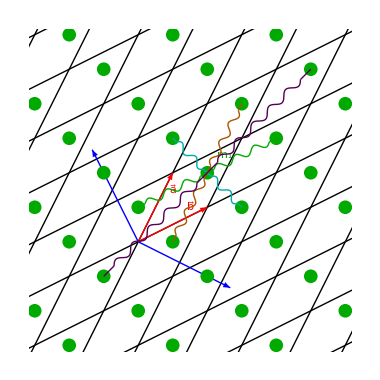

```mathematica
Module[{ld, cd, u, kArray},
u = { {1/2,1}, {1,1/2}, {1/2,3} } ;
ld = locDependent[ u, 1,{10} ]  ;
kArray = constructKArray[ 1 ] ;
cd = calculateCouplings[ ld, kArray ] ;
plotSprings[u, ld, cd, 1, 1, 1 ] 
]
```